```mathematica
thresholdNetwork=NetChain[{LinearLayer[10, "Input"-> 10],ElementwiseLayer[If[#>0,1,0]&] }];
initializedThresholdNetwork=NetInitialize[thresholdNetwork, Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[initializedThresholdNetwork,{1,"Weights"}]]];
```

Spearman Correlation: 0.209011

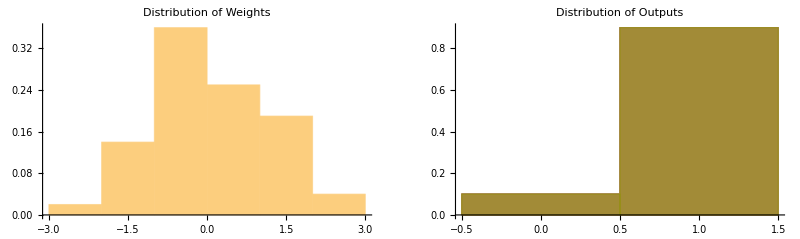

```mathematica
numSamples=10;
sampleInputs=ConstantArray[ConstantArray[0,10],numSamples];
outputs=initializedThresholdNetwork/@sampleInputs;
spearmanCorr=SpearmanRho[Flatten[Normal[weights]],Flatten[outputs]];
binnedWeights=BinLists[weights,10];
binnedOutputs=BinLists[Flatten[outputs],10];
Print["Spearman Correlation: ",spearmanCorr];
weightsHistogram=Histogram[weights,Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"];
outputsHistogram=Histogram[outputs,Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"];
GraphicsGrid[{{weightsHistogram,outputsHistogram}}]
```

```mathematica
flattenedOutputs = Flatten[outputs]
(*Bin weights and outputs*)binnedWeights=BinCounts[weights,{numBins}];
binnedOutputs=BinCounts[flattenedOutputs,{numBins}];

(*Joint binning for weights and outputs*)
jointBinned=BinCounts[Transpose[{weights,flattenedOutputs}],{numBins,numBins}];

(*Convert binned counts to probabilities*)
weightsProbDist=binnedWeights/Total[binnedWeights];
outputsProbDist=binnedOutputs/Total[binnedOutputs];
jointProbDist=jointBinned/Total[jointBinned];

(*Compute entropies*)
entropyWeights=-Total[weightsProbDist Log[weightsProbDist+10^-10]];
entropyOutputs=-Total[outputsProbDist Log[outputsProbDist+10^-10]];
entropyJoint=-Total[Flatten[jointProbDist] Log[Flatten[jointProbDist]+10^-10]];

(*Calculate mutual information*)
mutualInformation=entropyWeights+entropyOutputs-entropyJoint;

(*Output the result*)
mutualInformation
```

## Testing with constant biases

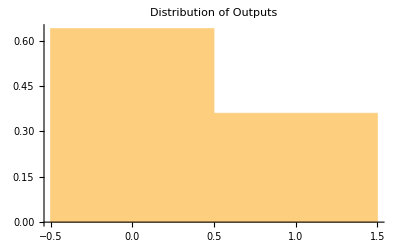

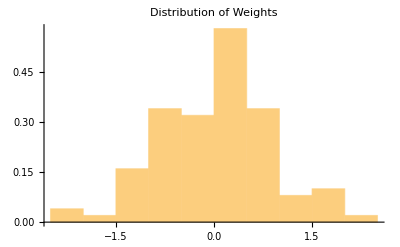

```mathematica
constantBias=0; (*Example constant bias value*)

thresholdNetwork=NetChain[{LinearLayer[10,"Input"->10],ElementwiseLayer[If[#>0,1,0]&]}];

(*Initialize the network with random weights and biases*)
initializedThresholdNetwork=NetInitialize[thresholdNetwork,Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];

(*Extract the linear layer from the initialized network*)
linearLayer=NetExtract[initializedThresholdNetwork,1];

(*Replace the biases in the linear layer with the constant value*)
linearLayerWithConstantBias=NetReplacePart[linearLayer,"Biases"->ConstantArray[constantBias,10]];

(*Reconstruct the network with the modified linear layer*)
initializedThresholdNetworkWithConstantBias=NetReplacePart[initializedThresholdNetwork,1->linearLayerWithConstantBias];
numSamples=10;
sampleInputs=RandomVariate[NormalDistribution[],{numSamples,10}];
outputs=initializedThresholdNetworkWithConstantBias/@sampleInputs;
Histogram[Flatten[outputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"]
Histogram[Flatten[weights],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"]
```

## Testing with Normal Distributions of Inputs, Weights, and Biases

```mathematica
thresholdNetwork=NetChain[{LinearLayer[10, "Input"-> 10],ElementwiseLayer[If[#>0,1,0]&] }];
initializedThresholdNetwork=NetInitialize[thresholdNetwork, Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];
weights=Flatten[Normal[NetExtract[initializedThresholdNetwork,{1,"Weights"}]]];
biases=Flatten[Normal[NetExtract[initializedThresholdNetwork,{1,"Biases"}]]];
```

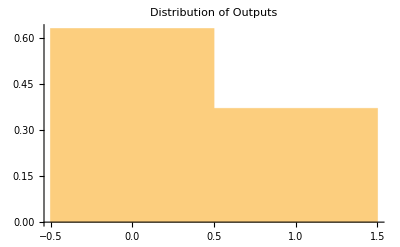

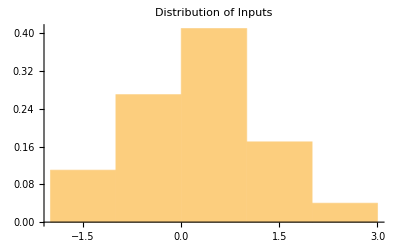

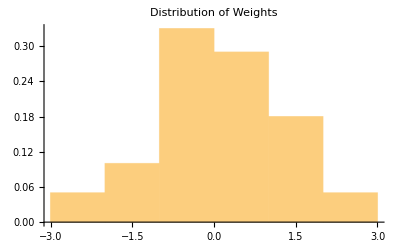

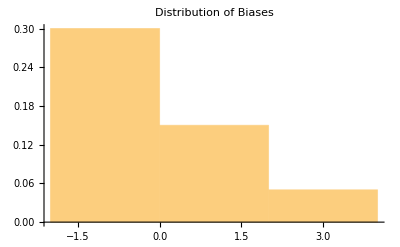

```mathematica
numSamples=10;
sampleInputs=RandomVariate[NormalDistribution[],{numSamples,10}];
outputs=initializedThresholdNetworkWithConstantBias/@sampleInputs;
Histogram[Flatten[outputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"]
Histogram[Flatten[sampleInputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Inputs"]
Histogram[Flatten[weights],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"]
Histogram[Flatten[biases],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Biases"]
```

## Activation Function

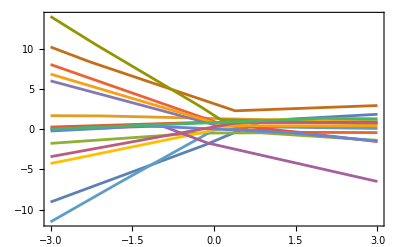
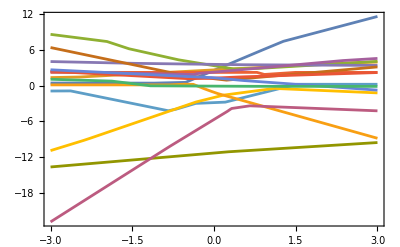
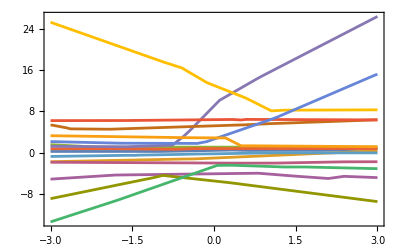
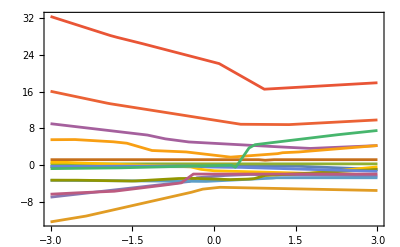
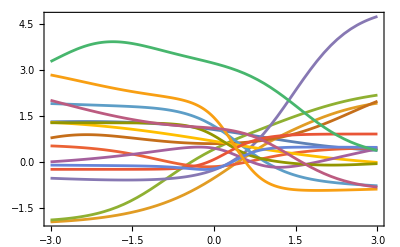
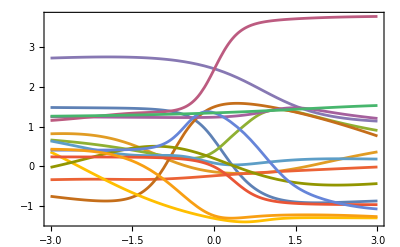
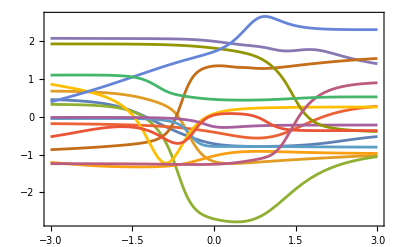
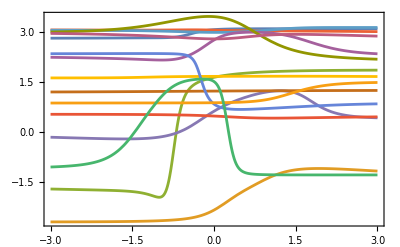
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{netPlots={{"[◼]", "NetGraphPlot"}}[NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[4]},
SeedRandom[1234];
Grid[
Append[Prepend[netPlots,""]]@Table[
Prepend[Text[act]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},
Plot[Evaluate@Flatten@Table[
Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->NormalDistribution[],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},
f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]
],
15
],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None
]
],{depth,{1,2,3,4}}
],{act,{Ramp,Tanh,Sin}}
]
]
]
```